ToDo:  
Figure out how to choose gamma.  One idea is that we balance the contribution of the non-beta term with the beta term so that each contributes equally to the reward function (easy to do).  A more convincing method would be to find a point where the policy is halfway between the beta=0 and beta=large policies (not so easy).

Try to add new features and remove features.  This must be done after we settle on value for beta.  Use correlation matrix for states to determine best candidates for removal.

Eventually (after first iteration), need to figure out when random-help policy should be applied.  If we only choose optimal help based on current best guess, we may not explore parts of policy-space vs. state that need exploring.  As we increase the amount of data, the fraction of time we use the random policy should decrease.  We need some estimate of the probability that the second-best policy is, in fact, the best policy.

On logistic vs. step:  The distance of a point in feature space to the hyperplane has no meaning since we have not formulated a metric in that space.  Using a logistic function of the distance between point and the hyperplane (function linearPolicy) thus doesn't make much sense.  The Budinich paper uses the logistic but only as a numerical trick.  In our numerical experiments, the global fit routines performed much better than the gradient-based routines anyway so the main motivation for this numerical trick doesn't apply.  [Note that the whole discussion of choosing beta in the Budinich paper is nonsense anyway since it is equivalent to rescaling the equation for the hyperplane.]

```mathematica
SetDirectory[NotebookDirectory[]]
```

SetDirectory::fstr: File specification  is not a string of one or more characters.

SetDirectory[]

### State

```mathematica
Dimensions[state=Import["state-uwplatt.csv"]]
```

{22226,10}

```mathematica
state[[1]]
```

{ttID,logSessionTime,fracSessionFlounderTime,logNowRedTrans,logNowRedTime,logNowIdleTime,sessionCorrect,sessionIncorrect,sessionHelp,fracSessionCorrect}

```mathematica
{3.137926039257166,0.0,-1,-1,-1,0,0,0,0,-1}
```

Create hash table for fast lookup

```mathematica
Map[(state1[#[[1]]]=Rest[#])&,Rest[state]];
nFeatures=Length[Rest[state[[1]]]]
```

9

### Reward

```mathematica
Dimensions[reward=Import["reward-0.5-md5:e2ed3385.csv"]]
```

{59,10}

```mathematica
Dimensions[reward=Import["reward-0.5-uwplatt-2Y130.csv"]]
```

{812,12}

```mathematica
Dimensions[reward=Import["reward-0-uwplatt.csv"]]
```

{7093,12}

```mathematica
Dimensions[reward=Import["reward-0.5-uwplatt.csv"]]
```

{7093,12}

```mathematica
Dimensions[reward=Import["reward-1-uwplatt.csv"]]
```

{7093,12}

This must be reset any time a reward file is loaded :

```mathematica
Clear[rewardPosition];rewardPosition[x_]:=rewardPosition[x]=First[First[Position[reward[[1]],x,1,1]]];
rewardValue[x_,y_]:=x[[rewardPosition[y]]]
```

```mathematica
reward[[1]]
```

{KC,clientID,ttID,stepTrans,learning,noSlip,spontaneous-hint,no-hints,GIVE-BACKWARDS-HINTS,forwards-hint,zz-unclassified-hint,zz-extra-hint}

### Evaluate State & Reward

```mathematica
Map[Histogram[Rest[#],PlotLabel->First[#],PlotRange->All]&,Transpose[Map[Rest,state]]]
```

```mathematica
TableForm[Correlation[Map[Rest,Rest[state]]],TableHeadings->{Rest[state[[1]]],Rest[state[[1]]]}]
```

| logSessionTime | fracSessionFlounderTime | logNowRedTrans | logNowRedTime | logNowIdleTime | sessionCorrect | sessionIncorrect | sessionHelp | fracSessionCorrect
logSessionTime | 1. | 0.472239 | 0.307646 | 0.292993 | 0.0736642 | 0.721848 | 0.642297 | 0.501846 | -0.417251
fracSessionFlounderTime | 0.472239 | 1. | 0.533426 | 0.444699 | 0.107798 | 0.0601547 | 0.41525 | 0.166245 | -0.657447
logNowRedTrans | 0.307646 | 0.533426 | 1. | 0.910976 | -0.0126933 | 0.00190302 | 0.260697 | 0.236816 | -0.551276
logNowRedTime | 0.292993 | 0.444699 | 0.910976 | 1. | 0.102849 | -0.0102855 | 0.207888 | 0.161136 | -0.541808
logNowIdleTime | 0.0736642 | 0.107798 | -0.0126933 | 0.102849 | 1. | -0.0444632 | -0.0232201 | -0.150746 | -0.0172625
sessionCorrect | 0.721848 | 0.0601547 | 0.00190302 | -0.0102855 | -0.0444632 | 1. | 0.661039 | 0.489532 | -0.0344468
sessionIncorrect | 0.642297 | 0.41525 | 0.260697 | 0.207888 | -0.0232201 | 0.661039 | 1. | 0.397376 | -0.319528
sessionHelp | 0.501846 | 0.166245 | 0.236816 | 0.161136 | -0.150746 | 0.489532 | 0.397376 | 1. | -0.26693
fracSessionCorrect | -0.417251 | -0.657447 | -0.551276 | -0.541808 | -0.0172625 | -0.0344468 | -0.319528 | -0.26693 | 1.

List different policy combinations and number of instances of each

```mathematica
Block[{pp=Map[Drop[#,6]&,Rest[reward]]},Map[{#,Count[pp,#]}&,Union[pp]]]
```

{{{0,0,0,0,0,1},2},{{0,0,0,0,1,0},289},{{0,0,0,1,0,0},555},{{0,0,1,0,0,0},172},{{0,0,1,0,1,0},1},{{0,1,0,0,0,0},3638},{{1,0,0,0,0,0},2018},{{1,0,0,1,0,0},361},{{1,0,1,0,0,0},56}}

### Analyze routines

Policy choice is represented by a 0 or 1; -1 means policy doesn' t apply.  There is some nonsense in Budinich paper about -1 & 1 being preferred, but Eqn. (2) in paper is effectively the same for either convention.

```mathematica
policyVector[x_]:={Which[rewardValue[x,"no-hints"]==1,0,rewardValue[x,"spontaneous-hint"]==1,1,True,-1],
Which[rewardValue[x,"GIVE-BACKWARDS-HINTS"]==1,1,rewardValue[x,"forwards-hint"]==1,0,True,-1]};
policyVector[x_,y_]:=policyVector[x][[y]];
nPolicies=2;  (* Number of policies *)
comparePolicies[x_,y_]:=If[x===-1||y===-1,0,(x-y)^2] (* For policy to not apply, -1 must be explicit *);
invertPolicy[x_]:=If[x<0,x,1-x]
```

```mathematica
useStep=True; (* Choose between step function and a logistic *)
linearPolicy[state_,x_]:=Block[{a=Drop[x,-1],b=x[[-1]]},Block[{h=a.state+b  (* divide this by Sqrt[a.a] to get distance of state from hyperplane. *)},If[ useStep,(Sign[h]+1)/2,(Tanh[h/(2 Sqrt[a.a])]+1)/2]]]
```

Maybe should have weight for integrated probability (probability student has already learned skill before this step).

```mathematica
rewardFunctionTerm[beta_,x_,policy_,r_]:= 
Block[{pp=linearPolicy[state1[r[[3]]],x]},If[r[[4]]>0 ,(r[[5]]+beta r[[6]])/r[[4]] comparePolicies[pp,policyVector[r,policy]],0]];
rewardFunction[beta_,x_]:=Sum[rewardFunction[beta,x[[i]],i],{i,nPolicies}];rewardFunction[beta_,x_,policy_]:=Apply[Plus,Map[rewardFunctionTerm[beta,x,policy,#]&,Rest[reward]]]
```

```mathematica
globalMinimum=True; (* Find global minimum or use gradient method for local *)
minimizer[fcn_,xx_,opts___]:=If[globalMinimum,NMinimize[fcn,xx,opts],FindMinimum[fcn,Map[{#,(Random[]-0.5)}&,xx],opts]];
minit[beta_,policy_,opts___]:=Block[{xx=Table[x[i],{i,nFeatures+If[useStep,0,1]}],zz,zzz,yy,yyy},
If[useStep,
(* Try each side of hyperplane and take best fit.  Use b=-1 or +1 as normalization. *)
yy=Append[xx,1];
zz=minimizer[rewardFunction[beta,yy,policy],xx,opts];
yyy=Append[xx,-1];
zzz=minimizer[rewardFunction[beta,yyy,policy],xx,opts];
	If[First[zzz]<First[zz],zz=zzz;yy=yyy],
(* For logistic, b is a fit parameter. *) 
yy=xx;zz=minimizer[rewardFunction[beta,yy,policy],xx,opts]];{First[zz],yy/.zz[[2]]}];
(* Add up the contribution from each policy to the reward function *)
minP[beta_,opts___]:=Block[{mp=Table[minit[beta,i,opts],{i,nPolicies}]},{Apply[Plus,Map[First,mp]],Map[#[[2]]&,mp]}]
```

Count, for each step where a policy choice can be made, number of instances of each policy choice or pair of policy choices.  If input is not a list, use original choice taken by Andes.

```mathematica
getPolicyVector[x_,r_]:=If[Head[x]===List,Map[linearPolicy[state1[r[[3]]],#]&,If[MatrixQ[x],x,Partition[x,nFeatures+1]]],policyVector[r]];
dist[x_]:=Block[{y=Map[getPolicyVector[x,#]&,Rest[reward]]},TableForm[Map[Count[y,#]&,Union[y]],TableHeadings->{Union[y],None}]];
dist[x_,y_]:=Block[{z=Map[{getPolicyVector[x,#],getPolicyVector[y,#]}&,Rest[reward]],hx,hy},hx=Union[Map[#[[1]]&,z]];hy=Union[Map[#[[2]]&,z]];TableForm[Outer[Count[z,{#1,#2}]&,hx,hy,1],TableHeadings->{hx,hy}]]
```

### Reward for a given state

```mathematica
inState=Drop[{3.137926039257166,0.,-1,-1,-1,0,0,0,0,-1},-1]
```

{3.13793,0.,-1,-1,-1,0,0,0,0}

```mathematica
Dimensions[model={{2.538800860156868,2.2803328747460023,3.14590147370558,0.018859458291908493,-3.9811501134507585,1.9844137181914405,-1.5409915433978683,-0.7212502973981954,4.7746864538535405,1},{0.5619599468110025,-3.170146371240845,-5.469995221644137,-6.320867938876214,-4.291569798230821,-2.9339618036379775,-3.553157996114464,3.742046728947423,5.0077662607773235,1}}]
```

{2,10}

```mathematica
Map[linearPolicy[inState,#]&,model]
```

{1,1}

### Analyze

Calculate random data point

```mathematica
rewardFunction[1/8,Table[(Random[]-0.5)*10,{nPolicies},{nFeatures+1}]]
```

40.3118

```mathematica
vals=Table[rewardFunction[1/8,Table[(Random[]-0.5)*10,{nPolicies},{nFeatures+1}]],{500}];
```

```mathematica
{Min[vals],Mean[vals],Histogram[vals]}
```

{2.48894,4.39738,-Graphics-}

```mathematica
Block[{useStep=False},rewardFunction[1.0,Table[(Random[]-0.5)*10,{nPolicies},{nFeatures+1}]]]
```

66.9703

```mathematica
Timing[Block[{useStep=False},soln1=minP[1.0]]]
```

{83.7043,{39.7684,{{-88559.3,285696.,278649.,-22742.3,-102300.,-58643.5,1052.94,29744.5,2.999×10^6,-874736.},{-6.33428×10^6,2.35502×10^7,9.49214×10^6,-2.72467×10^6,8.92862×10^6,-1.44261×10^6,-325496.,639641.,-572732.,-1.583×10^7}}}}

```mathematica
Timing[soln1=minP[1/10,Method->"DifferentialEvolution"]]
```

{330.883,{24.342,{{0.684948,2.31651,3.62204,-1.49226,0.382315,3.27751,-2.96753,0.0745606,-0.999623,1},{0.106957,-0.000558429,-3.29267,-1.56657,-0.232296,0.540993,-0.684705,0.368498,2.35265,1}}}}

```mathematica
dist[0]
```

{-1,-1} | 20
{-1,0} | 33
{-1,1} | 17
{0,-1} | 459
{1,-1} | 282

```mathematica
dist[soln1[[2]]]
```

{0,0} | 355
{0,1} | 264
{1,0} | 123
{1,1} | 69

### Different values of beta (step)

#### Calculate solutions

```mathematica
Timing[soln[0]=minP[0,Method->"DifferentialEvolution"]]
```

{261.785,{18.8955,{{1.32029,-0.187193,2.87475,1.47354,-1.41357,1.98788,-0.999332,-0.947706,2.41297,-1},{-0.270995,0.631365,-0.267374,-0.423571,-0.536584,-0.68077,-1.01494,0.938748,0.820445,1}}}}

```mathematica
Timing[soln[1/32]=minP[1/32,Method->"DifferentialEvolution"]]
```

{464.376,{20.314,{{1.2713,-1.65623,2.84577,0.414301,-1.11311,0.183197,-0.396718,-1.06074,3.0045,-1},{-0.270995,0.631365,-0.267374,-0.423571,-0.536584,-0.68077,-1.01494,0.938748,0.820445,1}}}}

```mathematica
Timing[soln[1/16]=minP[1/16,Method->"DifferentialEvolution"]]
```

{388.659,{21.6459,{{-0.0569769,1.24985,3.6341,-0.472825,-0.527584,2.0234,-0.748981,-1.17842,1.99004,1},{-0.270995,0.631365,-0.267374,-0.423571,-0.536584,-0.68077,-1.01494,0.938748,0.820445,1}}}}

```mathematica
Timing[soln[1/12]=minP[1/12,Method->"DifferentialEvolution"]]
```

{402.445,{22.8595,{{2.5388,2.28033,3.1459,0.0188595,-3.98115,1.98441,-1.54099,-0.72125,4.77469,1},{0.56196,-3.17015,-5.47,-6.32087,-4.29157,-2.93396,-3.55316,3.74205,5.00777,1}}}}

```mathematica
Timing[soln[1/8]=minP[0.125,Method->"DifferentialEvolution"]]
```

{385.395,{24.7691,{{-0.0587511,2.03442,6.85645,-1.78348,-0.118097,1.9199,-1.22898,-0.987826,5.40652,1},{-0.270995,0.631365,-0.267374,-0.423571,-0.536584,-0.68077,-1.01494,0.938748,0.820445,1}}}}

```mathematica
Timing[soln[1/4]=minP[0.25,Method->"DifferentialEvolution"]]
```

{535.822,{31.9148,{{-1.3468,-0.0199659,6.77,-1.05188,1.07692,9.78643,-6.8881,-0.272425,6.25266,-1},{1.37119,6.69393,-2.58596,-2.28234,-2.90732,-1.26481,-1.81397,0.284135,-1.38193,1}}}}

```mathematica
Timing[soln[1/2]=minP[0.5,Method->"DifferentialEvolution"]]
```

{526.69,{44.1291,{{-1.02836,2.19708,3.76468,-0.998413,1.62745,-0.138661,-1.64438,0.308879,4.58097,-1},{2.87706,-11.6199,-6.4731,-6.64163,-1.98941,-8.32764,-3.3499,1.9436,-0.272629,1}}}}

```mathematica
Timing[soln[1]=minP[1.0,Method->"DifferentialEvolution"]]
```

{481.776,{66.4251,{{-0.431456,0.712978,4.98544,-1.09486,0.773938,-0.56962,-2.90152,-2.03558,8.36525,1},{0.621415,-2.37209,0.0839235,-1.27393,2.68018,-4.23446,-1.98663,0.937442,-5.04946,-1}}}}

```mathematica
betaList={0,1/32,1/16,1/12,1/8,1/4,1/2,1};
```

```mathematica
Block[{file="soln-0.5-uwplatt.m"},If[FileExistsQ[file],DeleteFile[file]];Save[file,{soln,betaList}]]
```

#### Analyze Solutions

```mathematica
Get["soln-0.5-uwplatt.m"];
```

```mathematica
Export["junk.dat",soln[1/12][[2]]]
```

junk.dat

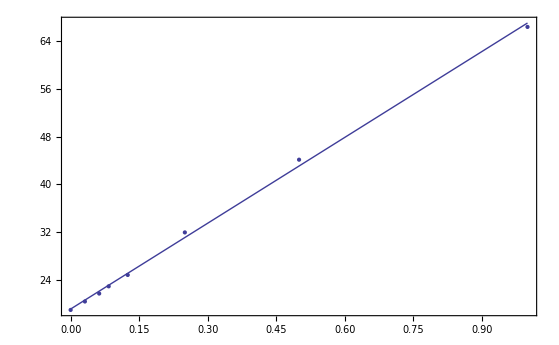

```mathematica
Block[{pp=Map[{#,First[soln[#]]}&,betaList],y},y=Fit[pp,{1,x},x];Show[ListPlot[pp,PlotRange->All,Axes->False,Frame->True],Plot[y,{x,0,1}]]]
```

```mathematica
Map[{#,soln[#][[1]],dist[soln[#][[2]]]}&,betaList]
```

{{0,18.8955,{0,0} | 3128
{0,1} | 215
{1,0} | 3704
{1,1} | 45},{1/32,20.314,{0,0} | 3603
{0,1} | 248
{1,0} | 3229
{1,1} | 12},{1/16,21.6459,{0,0} | 4539
{0,1} | 258
{1,0} | 2293
{1,1} | 2},{1/12,22.8595,{0,0} | 4687
{0,1} | 194
{1,0} | 2047
{1,1} | 164},{1/8,24.7691,{0,0} | 5039
{0,1} | 255
{1,0} | 1793
{1,1} | 5},{1/4,31.9148,{0,0} | 5768
{0,1} | 82
{1,0} | 1175
{1,1} | 67},{1/2,44.1291,{0,0} | 6566
{0,1} | 180
{1,0} | 195
{1,1} | 151},{1,66.4251,{0,0} | 6398
{0,1} | 406
{1,0} | 174
{1,1} | 114}}

Compare solutions for different beta values

```mathematica
Map[{#,dist[soln[0][[2]],soln[#][[2]]]}&,betaList]
```

{{0, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 3128 | 0 | 0 | 0
{0,1} | 0 | 215 | 0 | 0
{1,0} | 0 | 0 | 3704 | 0
{1,1} | 0 | 0 | 0 | 45},{1/32, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 2970 | 0 | 158 | 0
{0,1} | 0 | 215 | 0 | 0
{1,0} | 633 | 0 | 3071 | 0
{1,1} | 0 | 33 | 0 | 12},{1/16, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 3093 | 0 | 35 | 0
{0,1} | 0 | 215 | 0 | 0
{1,0} | 1446 | 0 | 2258 | 0
{1,1} | 0 | 43 | 0 | 2},{1/12, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 3000 | 61 | 25 | 42
{0,1} | 46 | 132 | 1 | 36
{1,0} | 1637 | 0 | 1999 | 68
{1,1} | 4 | 1 | 22 | 18},{1/8, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 3073 | 0 | 55 | 0
{0,1} | 0 | 215 | 0 | 0
{1,0} | 1966 | 0 | 1738 | 0
{1,1} | 0 | 40 | 0 | 5},{1/4, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 2978 | 72 | 68 | 10
{0,1} | 172 | 5 | 32 | 6
{1,0} | 2597 | 5 | 1055 | 47
{1,1} | 21 | 0 | 20 | 4},{1/2, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 2928 | 147 | 0 | 53
{0,1} | 180 | 11 | 23 | 1
{1,0} | 3429 | 19 | 161 | 95
{1,1} | 29 | 3 | 11 | 2},{1, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 2930 | 146 | 5 | 47
{0,1} | 198 | 17 | 0 | 0
{1,0} | 3244 | 226 | 167 | 67
{1,1} | 26 | 17 | 2 | 0}}

### Try different methods (logistic)

Values for beta = 1.0, looks like NelderMead is fastest, although several methods find minimum.  It seems that minimum occurs for assumption that points are "far away" from the hyperplane in most methods.

```mathematica
Timing[Block[{useStep=False},soll["NelderMead"]=minP[1.0,Method->"NelderMead"]]]
```

{36.0085,{16.3563,{{-7.21134,-87.7897,-74.8709,17.5994,13.9983,12.6471,-2.64573,8.18302,-71.8016,-58.2385},{6.6533×10^18,2.15421×10^18,-1.29817×10^18,1.87021×10^18,-1.64179×10^18,-1.17187×10^18,-3.49781×10^17,1.68807×10^17,-1.02098×10^18,-3.77123×10^19}}}}

```mathematica
rewardFunction[1.0,soll["NelderMead"][[2]]]
```

25.6811

```mathematica
Timing[Block[{useStep=False},soll["DifferentialEvolution"]=minP[1.0,Method->"DifferentialEvolution"]]]
```

{124.155,{16.3563,{{-894.738,-10892.4,-9289.51,2183.62,1736.83,1569.17,-328.265,1015.3,-8908.69,-7225.87},{3.86481×10^10,1.25135×10^10,-7.54088×10^9,1.08638×10^10,-9.5369×10^9,-6.80723×10^9,-2.03183×10^9,9.80576×10^8,-5.93073×10^9,-2.19066×10^11}}}}

```mathematica
rewardFunction[1.0,soll["DifferentialEvolution"][[2]]]
```

25.6811

```mathematica
Timing[Block[{useStep=False},soll["SimulatedAnnealing"]=minP[1.0,Method->"SimulatedAnnealing"]]]
```

{37.7433,{16.3958,{{-300.413,604.133,-611.798,181.833,154.486,102.093,-21.4571,78.501,871.37,-206.964},{1.20866×10^6,391340.,-235829.,339748.,-298252.,-212885.,-63542.2,30666.,-185474.,-6.85093×10^6}}}}

```mathematica
rewardFunction[1.0,soll["SimulatedAnnealing"][[2]]]
```

26.7535

```mathematica
Timing[Block[{useStep=False},soll["RandomSearch"]=minP[1.0,Method->"RandomSearch"]]]
```

{460.248,{16.3563,{{-449171.,-5.46814×10^6,-4.66347×10^6,1.09621×10^6,871911.,787744.,-164794.,509694.,-4.47229×10^6,-3.62749×10^6},{181.921,58.9024,-35.4957,51.1371,-44.8912,-32.0424,-9.56404,4.61568,-27.9166,-1031.17}}}}

```mathematica
rewardFunction[1.0,soll["RandomSearch"][[2]]]
```

25.6811

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["ConjugateGradient"]=minP[1.0,Method->"ConjugateGradient"]]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{7.41887,{16.4934,{{-0.117327,-0.724784,-0.444027,0.0582239,0.0865167,0.103864,-0.0209483,0.0653712,-0.69816,0.118356},{0.746417,4.35628,-0.644905,1.2699,-1.21268,-0.692358,-0.191049,0.157696,-1.73913,-3.62826}}}}

```mathematica
rewardFunction[1.0,soll["ConjugateGradient"][[2]]]
```

26.3575

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["PrincipalAxis"]=minP[1.0,Method->"PrincipalAxis"]]]
```

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0, 0.12550865415375473`, 0, 0, 0, 0, 0, 0, 0, 0} from the point {-0.06563686017330356`, -0.12550865415375473`, 0.1901308758732626`, « 4 », -0.3999405286388935`, 0.40978328093989036`, 0.39338889979834435`}.

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0, 0.0583414738710753`, 0, 0, 0, 0, 0, 0, 0, 0} from the point {0.602164570687847`, -0.0583414738710753`, 0.46632136103184874`, « 4 », -0.2600226969467423`, 0.17432140426394016`, 0.14905154772989582`}.

{42.9585,{16.3637,{{-1.13015,-17.206,-14.4187,3.38176,2.69917,2.40965,-0.509591,1.57351,-13.4752,-12.6217},{1.20229×10^13,3.8896×10^12,-2.34274×10^12,3.37744×10^12,-2.96611×10^12,-2.11753×10^12,-6.31984×10^11,3.04912×10^11,-1.84414×10^12,-6.81447×10^13}}}}

```mathematica
rewardFunction[1.0,soll["PrincipalAxis"][[2]]]
```

25.6779

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["Newton"]=minP[1.0,Method->"Newton"]]]
```

FindMinimum::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

{23.9064,{16.3563,{{-0.000921532,-0.0112186,-0.00956771,0.00224902,0.00178884,0.00161616,-0.000338096,0.0010457,-0.00917548,-0.00744227},{0.487405,0.157812,-0.0951008,0.137007,-0.120273,-0.0858485,-0.0256241,0.0123664,-0.0747946,-2.76272}}}}

```mathematica
rewardFunction[1.0,soll["Newton"][[2]]]
```

25.6811

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["QuasiNewton"]=minP[1.0,Method->"QuasiNewton"]]]
```

FindMinimum::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{4.19636,{16.5817,{{-0.16525,-2.01173,-1.71569,0.403295,0.320776,0.289811,-0.0606276,0.187516,-1.64535,-1.33455},{2.90553×10^7,1.10566×10^7,5.41676×10^7,-9.9772×10^6,-5.97041×10^6,-3.46695×10^7,-792364.,658332.,-1.28151×10^7,-2.17306×10^7}}}}

```mathematica
rewardFunction[1.0,soll["QuasiNewton"][[2]]]
```

25.0931

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["InteriorPoint"]=minP[1.0,Method->"InteriorPoint"]]]
```

{29.2326,{16.3958,{{-0.00146663,0.00294941,-0.00298683,0.000887716,0.00075421,0.000498422,-0.000104755,0.000383245,0.00425407,-0.00101041},{0.0141712,0.00458837,-0.00276504,0.00398347,-0.00349693,-0.00249603,-0.000745018,0.000359551,-0.00217464,-0.0803256}}}}

```mathematica
rewardFunction[1.0,soll["InteriorPoint"][[2]]]
```

26.7535

### Try different methods (step)

Values for beta = 1.0, looks like DifferentialEvolution is the winner.  Also, the local (gradient-based) methods don't do so well, as expected.

```mathematica
Timing[minP[1.0,Method->"NelderMead"]]
```

{6.598,{8.13389,{{-1.30833,1.20292,0.0541532,-0.312908,1.18482,0.575998,-1.18559,-2.04429,0.722779,-1},{0.0193294,0.237726,-0.10374,1.48614,0.998219,-0.140727,-0.930155,1.16015,-1.0486,-1}}}}

```mathematica
Timing[minP[1.0,Method->"DifferentialEvolution"]]
```

{53.7838,{7.25327,{{0.458872,0.88279,2.33705,-0.87639,-0.125391,-0.399425,-0.741103,-0.147854,3.00794,1},{-0.0281669,0.0369702,-0.943118,1.10431,1.32096,0.184703,-1.52032,1.83936,-0.0720281,1}}}}

```mathematica
Timing[minP[1.0,Method->"SimulatedAnnealing"]]
```

{6.86796,{7.77481,{{0.81736,0.506017,0.815032,-2.23944,-0.649892,-0.597675,-0.227291,-0.710239,-1.23265,-1},{1.23769,-0.417668,0.039154,-0.0952646,0.793909,-0.175988,-1.04153,0.965019,-1.80281,1}}}}

```mathematica
Timing[minP[1.0,Method->"RandomSearch"]]
```

{22.2306,{8.10895,{{0.501366,-0.254619,-0.680623,-0.812779,0.519202,-0.552089,-0.52888,-0.0861353,0.0111569,-1},{-0.945951,0.961341,-0.479345,0.410781,-0.393891,0.317801,-0.233057,0.483033,-0.607396,1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"ConjugateGradient"]]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

{0.565914,{13.9099,{{0.325332,0.0169767,-0.282905,-0.0719721,-0.204668,-0.0367029,0.426265,0.403656,-0.421964,-1},{-0.201927,-0.134271,0.488831,-0.00618267,0.0167314,-0.490621,-0.256299,-0.292898,0.362193,1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"PrincipalAxis"]]]
```

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0.1572711413405215`, 0, 0, 0, 0, 0, 0, 0, 0} from the point {-0.1572711413405215`, -0.48523038537073004`, 0.06995423589046401`, « 3 », 0.22013929518413133`, -0.470324265063964`, 0.3278983830302593`}.

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0.11703350667909285`, 0, 0, 0, 0, 0, 0, 0, 0} from the point {-0.11703350667909285`, 0.2739806610787161`, 0.2200242438208383`, « 3 », 0.40419008197526274`, 0.3892426907449058`, -0.08173378814745269`}.

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0, 0.2045421323828221`, 0, 0, 0, 0, 0, 0, 0} from the point {0.363539824368996`, -0.2045421323828221`, 0.04047337539723228`, « 3 », -0.30225548326224616`, 0.39259779856464183`, 0.18527565343682184`}.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

{1.13283,{8.08503,{{-4.41546,0.374362,-0.686092,-0.0754918,0.380466,-0.177092,0.226681,0.487385,0.239814,1},{-0.146264,0.436204,0.308554,-0.195268,-0.383991,-0.451148,0.0194448,0.326483,1.16631,-1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"Newton"]]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

{0.808877,{14.082,{{0.455702,0.485545,0.391308,0.0287001,-0.372663,0.499285,0.338972,0.0124547,-0.00595225,1},{-0.187902,-0.131631,-0.159031,0.36609,0.299644,0.374321,-0.369801,-0.313145,0.118159,-1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"QuasiNewton"]]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

{0.559915,{8.60977,{{-0.300012,-0.0332556,-0.179265,0.257802,0.359734,0.261682,-0.491363,-0.110566,0.0187657,-1},{0.288327,0.0743471,-0.00108658,-0.364874,0.126794,-0.179161,-0.201075,0.168382,-0.193941,-1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"InteriorPoint"]]]
```

{1.27681,{10.5594,{{0.0630366,-0.0608091,0.4067,-0.202578,-0.326397,0.420425,-0.488891,-0.411571,0.158491,1},{-0.0210069,0.247402,-0.150297,-0.117185,-0.109436,-0.411089,0.317844,-0.419557,0.39297,-1}}}}

### Calculations for step model.

Expectation value for learning gain, 1-P(G)-P(s) in terms of: cbl = correct before learning, wbl = wrong before learning, cal = correct after learning, and wal = wrong after learning.

```mathematica
bind[x_,a_,b_]:=x^a (1-x)^b ((a+b+1)!)/(a! b!)
```

```mathematica
Integrate[bind[x,a,b],{x,0,1},Assumptions->{a>-1,b>-1}]
```

1

Find the expecation value for the learning gain.

```mathematica
1-Integrate[(g+s) bind[g,cbl,wbl] bind[s,wal,cal],{g,0,1},{s,0,1},Assumptions->{cbl>-1,wbl>-1,cal>-1,wal>-1}]
```

1-(1+wal)/(2+cal+wal)-(1+cbl)/(2+cbl+wbl)

Find the expecation value for the normalized learning gain (Hake gain).

```mathematica
1-Integrate[s/(1-g) bind[g,cbl,wbl] bind[s,wal,cal],{g,0,1},{s,0,1},Assumptions->{cbl>-1,wbl>0,cal>-1,wal>-1}]
```

1-((1+wal) (1+cbl+wbl))/((2+cal+wal) wbl)

```mathematica
FullSimplify[%]
```

1-((1+wal) (1+cbl+wbl))/((2+cal+wal) wbl)

Find the probability that learning has occurred (that is, find the probability that s+g<1).

```mathematica
int[cbl_,wbl_,cal_,wal_]:=Integrate[bind[g,cbl ,wbl] bind[ s,wal ,cal],{g,0,1},{s,0,1-g},Assumptions->{cbl>-1,wbl>-1,cal>-1,wal>-1}]
```

Recursion relation that produces same result:

```mathematica
Clear[f2];
f2[a_,b_,0,d_]:=(1+b+d)! (1+a+b)!/( b! (2+a+b+d)!);
f2[a_,b_,c_,d_]:=f2[a,b,c-1,d+1]+(c+d+1)! (a+c)! (a+b+1)! (b+d+1)!/((a+b+c+d+2)! a! b! c! (d+1)!)/;c>0
```

Use recursion and log factorial to test that this is stable.

```mathematica
Clear[f3];
f3[a_,b_,0,d_]:=Exp[N[Log[(1+b+d)!]]+N[Log[(1+a+b)!]]-N[Log[b!]]-N[Log[(2+a+b+d)!]]];
f3[a_,b_,c_,d_]:=f3[a,b,c-1,d+1]+Exp[N[Log[(c+d+1)!]]+N[Log[(a+b+1)!]]-N[Log[(a+b+c+d+2)!]]+N[Log[ (a+c)!]]-N[Log[a!]]-N[Log[ c!]]+N[Log[(b+d+1)!]] -N[Log[ b!]]-N[Log[ (d+1)!]]]/;c>0
```

Compare methods for small values.

```mathematica
Sort[Flatten[Table[{cbl,wbl,cal,wal,int[cbl,wbl,cal,wal]-f2[cbl,wbl,cal,wal]},{cbl,0,2},{wbl,0,2},{cal,0,2},{wal,0,2}],3]]
```

{{0,0,0,0,0},{0,0,0,1,0},{0,0,0,2,0},{0,0,1,0,0},{0,0,1,1,0},{0,0,1,2,0},{0,0,2,0,0},{0,0,2,1,0},{0,0,2,2,0},{0,1,0,0,0},{0,1,0,1,0},{0,1,0,2,0},{0,1,1,0,0},{0,1,1,1,0},{0,1,1,2,0},{0,1,2,0,0},{0,1,2,1,0},{0,1,2,2,0},{0,2,0,0,0},{0,2,0,1,0},{0,2,0,2,0},{0,2,1,0,0},{0,2,1,1,0},{0,2,1,2,0},{0,2,2,0,0},{0,2,2,1,0},{0,2,2,2,0},{1,0,0,0,0},{1,0,0,1,0},{1,0,0,2,0},{1,0,1,0,0},{1,0,1,1,0},{1,0,1,2,0},{1,0,2,0,0},{1,0,2,1,0},{1,0,2,2,0},{1,1,0,0,0},{1,1,0,1,0},{1,1,0,2,0},{1,1,1,0,0},{1,1,1,1,0},{1,1,1,2,0},{1,1,2,0,0},{1,1,2,1,0},{1,1,2,2,0},{1,2,0,0,0},{1,2,0,1,0},{1,2,0,2,0},{1,2,1,0,0},{1,2,1,1,0},{1,2,1,2,0},{1,2,2,0,0},{1,2,2,1,0},{1,2,2,2,0},{2,0,0,0,0},{2,0,0,1,0},{2,0,0,2,0},{2,0,1,0,0},{2,0,1,1,0},{2,0,1,2,0},{2,0,2,0,0},{2,0,2,1,0},{2,0,2,2,0},{2,1,0,0,0},{2,1,0,1,0},{2,1,0,2,0},{2,1,1,0,0},{2,1,1,1,0},{2,1,1,2,0},{2,1,2,0,0},{2,1,2,1,0},{2,1,2,2,0},{2,2,0,0,0},{2,2,0,1,0},{2,2,0,2,0},{2,2,1,0,0},{2,2,1,1,0},{2,2,1,2,0},{2,2,2,0,0},{2,2,2,1,0},{2,2,2,2,0}}

```mathematica
Block[{cbl=4,wbl=5,cal=24,wal=30},{N[f2[cbl,wbl,cal,wal],20],f2[cbl,wbl,cal,wal]-f3[cbl,wbl,cal,wal]}]
```

{0.48588058086310524853,1.25455×10^-14}

```mathematica
Block[{cbl=7,wbl=16,max=60},ListPlot3D[Table[f3[cbl,wbl,cal,wal],{cal,0,max},{wal,0,max}],AxesLabel->{"wal","cal","P"},PlotRange->{0,1}]]
```

Log of the diff between exact and numerical reveals that the recursion is stable.  It could be slightly improved by doing the recursion to the nearest edge.

```mathematica
Block[{cbl=7,wbl=16,max=60},ListPlot3D[Table[Log[10,Abs[f2[cbl,wbl,cal,wal]-f3[cbl,wbl,cal,wal]]],{cal,0,max},{wal,0,max}],AxesLabel->{"wal","cal","P"},PlotRange->All]]
```

```mathematica
Block[{cbl=7,wbl=8,max=20},ListContourPlot[Table[f3[cbl,wbl,cal,wal],{cal,0,max},{wal,0,max}],PlotRange->{0,1}]]
```

See who works for some confidence level.

```mathematica
Select[Flatten[Table[{cbl,wbl,cal,wal,f2[cbl,wbl,cal,wal]},{cbl,0,3},{wbl,0,3},{cal,0,3},{wal,0,3}],3],(#[[-1]]>.95)&]
```

{{0,2,3,0,34/35},{0,3,2,0,34/35},{0,3,3,0,69/70},{0,3,3,1,121/126},{1,3,3,0,121/126}}